```mathematica
g1[k1_,k2_,k3_]:=Cos[π/2 k1]Cos[π/2 k2]Cos[π/2 k3]-I Sin[π/2 k1]Sin[π/2 k2]Sin[π/2 k3];
g2[k1_,k2_,k3_]:=-Cos[π/2 k1]Sin[π/2 k2]Sin[π/2 k3]+I Sin[π/2 k1]Cos[π/2 k2]Cos[π/2 k3];
g3[k1_,k2_,k3_]:=-Sin[π/2 k1]Cos[π/2 k2]Sin[π/2 k3]+I Cos[π/2 k1]Sin[π/2 k2]Cos[π/2 k3];
g4[k1_,k2_,k3_]:=-Sin[π/2 k1]Sin[π/2 k2]Cos[π/2 k3]+I Cos[π/2 k1]Cos[π/2 k2]Sin[π/2 k3];
```

```mathematica
spMatrix={
{Es,0,0,0,Vss g1[k1,k2,k3],Vsp g2[k1,k2,k3],Vsp g3[k1,k2,k3],Vsp g4[k1,k2,k3]},
{0,Ep,0,0,-Vsp g2[k1,k2,k3],Vxx g1[k1,k2,k3],Vxy g4[k1,k2,k3],Vxy g3[k1,k2,k3]},
{0,0,Ep,0,-Vsp g3[k1,k2,k3],Vxy g4[k1,k2,k3], Vxx g1[k1,k2,k3], Vxy g2[k1,k2,k3]},
{0,0,0,Ep,-Vsp g4[k1,k2,k3],Vxy g3[k1,k2,k3],Vxy g2[k1,k2,k3],Vxx g1[k1,k2,k3]},
{Vss g1[k1,k2,k3]*,-Vsp g2[k1,k2,k3]*,-Vsp g3[k1,k2,k3]*,-Vsp g4[k1,k2,k3]*,Es,0,0,0},
{Vsp g2[k1,k2,k3]*,Vxx g1[k1,k2,k3]*,Vxy g4[k1,k2,k3]*,Vxy g3[k1,k2,k3]*,0,Ep,0,0},
{Vsp g3[k1,k2,k3]*,Vxy g4[k1,k2,k3]*,Vxx g1[k1,k2,k3]*,Vxy g2[k1,k2,k3]*,0,0,Ep,0},
{Vsp g4[k1,k2,k3]*,Vxy g3[k1,k2,k3]*,Vxy g2[k1,k2,k3]*,Vxx g1[k1,k2,k3]*,0,0,0,Ep}
};
```

```mathematica
(*Si*)
(*Es=0;
Ep=7.20;
Vss=-8.13;
Vsp=5.88;
Vxx=3.17;
Vxy=7.51;
*)
(*Ge*)
Es=0;
Ep=8.41;
Vss=-6.78;
Vsp=5.31;
Vxx=2.62;
Vxy=6.82;
```

```mathematica
Eigensystem[spMatrix/.{k1->0.2,k2->0,k3->0}]
```

{{11.6735,11.6735,11.0556,7.84533,-6.60199,5.1465,5.1465,4.52106},{{0.,0.,0.-0.456634 ⅈ,-0.539894,0.,0.,0.,-0.707107},{0.,0.,0.535623+0.0677776 ⅈ,-0.0573252+0.453021 ⅈ,0.,-6.66134×10^-16,0.701513+0.0887693 ⅈ,0.},{0.0221226-0.0621798 ⅈ,-0.66329-0.235988 ⅈ,-4.99029×10^-16-1.29446×10^-16 ⅈ,1.09483×10^-16-4.2207×10^-16 ⅈ,0.0221226-0.0621798 ⅈ,-0.66329-0.235988 ⅈ,1.43391×10^-16-4.38652×10^-17 ⅈ,0.},{-0.531574+0.085337 ⅈ,-0.0726624-0.452622 ⅈ,1.19464×10^-16+3.31344×10^-16 ⅈ,-2.80245×10^-16+1.01041×10^-16 ⅈ,0.531574-0.085337 ⅈ,0.0726624+0.452622 ⅈ,-6.71382×10^-17-1.30727×10^-17 ⅈ,0.},{-0.501564+0.494042 ⅈ,-0.0463137-0.0470188 ⅈ,-1.43735×10^-16+4.13778×10^-17 ⅈ,-3.49966×10^-17-1.21569×10^-16 ⅈ,-0.501564+0.494042 ⅈ,-0.0463137-0.0470188 ⅈ,-3.95762×10^-19-1.38132×10^-17 ⅈ,0.},{0.,0.,0.-0.456634 ⅈ,-0.539894,0.,0.,0.,0.707107},{0.,0.,0.535623-0.0677776 ⅈ,0.0573252+0.453021 ⅈ,0.,-6.66134×10^-16,-0.701513+0.0887693 ⅈ,0.},{-0.247884-0.385617 ⅈ,-0.452881+0.291123 ⅈ,3.84555×10^-16-1.63016×10^-16 ⅈ,1.37876×10^-16+3.2525×10^-16 ⅈ,0.247884+0.385617 ⅈ,0.452881-0.291123 ⅈ,-3.7533×10^-17+1.3517×10^-16 ⅈ,0.}}}

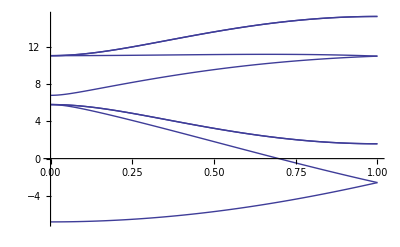

```mathematica
plot1=Plot[Sort[Eigenvalues[spMatrix/.{k1->x,k2->0,k3->0}]],{x,0,1}]
```

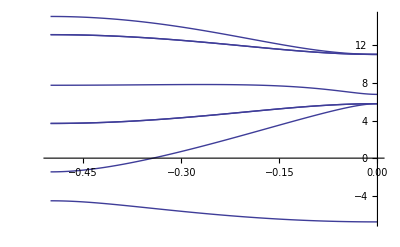

```mathematica
plot2=Plot[Sort[Eigenvalues[spMatrix/.{k1->x,k2->x,k3->x}]],{x,-0.5,0}]
```

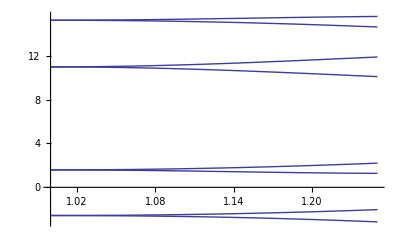

```mathematica
plot3=Plot[Sort[Eigenvalues[spMatrix/.{k1->1,k2->-(x-1),k3->x-1}]],{x,1,5/4}]
```

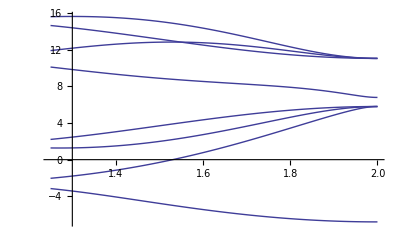

```mathematica
plot4=Plot[Sort[Eigenvalues[spMatrix/.{k1->3/4-(x-5/4),k2->-3/4+(x-5/4),k3->0}]],{x,5/4,2}]
```

```mathematica
MatrixForm[spMatrix]
```

(0 | 0 | 0 | 0 | -8.13 (Cos[(k1 π)/2] Cos[(k2 π)/2] Cos[(k3 π)/2]-ⅈ Sin[(k1 π)/2] Sin[(k2 π)/2] Sin[(k3 π)/2]) | 5.88 (ⅈ Cos[(k2 π)/2] Cos[(k3 π)/2] Sin[(k1 π)/2]-Cos[(k1 π)/2] Sin[(k2 π)/2] Sin[(k3 π)/2]) | 5.88 (ⅈ Cos[(k1 π)/2] Cos[(k3 π)/2] Sin[(k2 π)/2]-Cos[(k2 π)/2] Sin[(k1 π)/2] Sin[(k3 π)/2]) | 5.88 (-Cos[(k3 π)/2] Sin[(k1 π)/2] Sin[(k2 π)/2]+ⅈ Cos[(k1 π)/2] Cos[(k2 π)/2] Sin[(k3 π)/2])
0 | 7.2 | 0 | 0 | -5.88 (ⅈ Cos[(k2 π)/2] Cos[(k3 π)/2] Sin[(k1 π)/2]-Cos[(k1 π)/2] Sin[(k2 π)/2] Sin[(k3 π)/2]) | 3.17 (Cos[(k1 π)/2] Cos[(k2 π)/2] Cos[(k3 π)/2]-ⅈ Sin[(k1 π)/2] Sin[(k2 π)/2] Sin[(k3 π)/2]) | 7.51 (-Cos[(k3 π)/2] Sin[(k1 π)/2] Sin[(k2 π)/2]+ⅈ Cos[(k1 π)/2] Cos[(k2 π)/2] Sin[(k3 π)/2]) | 7.51 (ⅈ Cos[(k1 π)/2] Cos[(k3 π)/2] Sin[(k2 π)/2]-Cos[(k2 π)/2] Sin[(k1 π)/2] Sin[(k3 π)/2])
0 | 0 | 7.2 | 0 | -5.88 (ⅈ Cos[(k1 π)/2] Cos[(k3 π)/2] Sin[(k2 π)/2]-Cos[(k2 π)/2] Sin[(k1 π)/2] Sin[(k3 π)/2]) | 7.51 (-Cos[(k3 π)/2] Sin[(k1 π)/2] Sin[(k2 π)/2]+ⅈ Cos[(k1 π)/2] Cos[(k2 π)/2] Sin[(k3 π)/2]) | 3.17 (Cos[(k1 π)/2] Cos[(k2 π)/2] Cos[(k3 π)/2]-ⅈ Sin[(k1 π)/2] Sin[(k2 π)/2] Sin[(k3 π)/2]) | 7.51 (ⅈ Cos[(k2 π)/2] Cos[(k3 π)/2] Sin[(k1 π)/2]-Cos[(k1 π)/2] Sin[(k2 π)/2] Sin[(k3 π)/2])
0 | 0 | 0 | 7.2 | -5.88 (-Cos[(k3 π)/2] Sin[(k1 π)/2] Sin[(k2 π)/2]+ⅈ Cos[(k1 π)/2] Cos[(k2 π)/2] Sin[(k3 π)/2]) | 7.51 (ⅈ Cos[(k1 π)/2] Cos[(k3 π)/2] Sin[(k2 π)/2]-Cos[(k2 π)/2] Sin[(k1 π)/2] Sin[(k3 π)/2]) | 7.51 (ⅈ Cos[(k2 π)/2] Cos[(k3 π)/2] Sin[(k1 π)/2]-Cos[(k1 π)/2] Sin[(k2 π)/2] Sin[(k3 π)/2]) | 3.17 (Cos[(k1 π)/2] Cos[(k2 π)/2] Cos[(k3 π)/2]-ⅈ Sin[(k1 π)/2] Sin[(k2 π)/2] Sin[(k3 π)/2])
-8.13 Conjugate[Cos[(k1 π)/2] Cos[(k2 π)/2] Cos[(k3 π)/2]-ⅈ Sin[(k1 π)/2] Sin[(k2 π)/2] Sin[(k3 π)/2]] | -5.88 Conjugate[ⅈ Cos[(k2 π)/2] Cos[(k3 π)/2] Sin[(k1 π)/2]-Cos[(k1 π)/2] Sin[(k2 π)/2] Sin[(k3 π)/2]] | -5.88 Conjugate[ⅈ Cos[(k1 π)/2] Cos[(k3 π)/2] Sin[(k2 π)/2]-Cos[(k2 π)/2] Sin[(k1 π)/2] Sin[(k3 π)/2]] | -5.88 Conjugate[-Cos[(k3 π)/2] Sin[(k1 π)/2] Sin[(k2 π)/2]+ⅈ Cos[(k1 π)/2] Cos[(k2 π)/2] Sin[(k3 π)/2]] | 0 | 0 | 0 | 0
5.88 Conjugate[ⅈ Cos[(k2 π)/2] Cos[(k3 π)/2] Sin[(k1 π)/2]-Cos[(k1 π)/2] Sin[(k2 π)/2] Sin[(k3 π)/2]] | 3.17 Conjugate[Cos[(k1 π)/2] Cos[(k2 π)/2] Cos[(k3 π)/2]-ⅈ Sin[(k1 π)/2] Sin[(k2 π)/2] Sin[(k3 π)/2]] | 7.51 Conjugate[-Cos[(k3 π)/2] Sin[(k1 π)/2] Sin[(k2 π)/2]+ⅈ Cos[(k1 π)/2] Cos[(k2 π)/2] Sin[(k3 π)/2]] | 7.51 Conjugate[ⅈ Cos[(k1 π)/2] Cos[(k3 π)/2] Sin[(k2 π)/2]-Cos[(k2 π)/2] Sin[(k1 π)/2] Sin[(k3 π)/2]] | 0 | 7.2 | 0 | 0
5.88 Conjugate[ⅈ Cos[(k1 π)/2] Cos[(k3 π)/2] Sin[(k2 π)/2]-Cos[(k2 π)/2] Sin[(k1 π)/2] Sin[(k3 π)/2]] | 7.51 Conjugate[-Cos[(k3 π)/2] Sin[(k1 π)/2] Sin[(k2 π)/2]+ⅈ Cos[(k1 π)/2] Cos[(k2 π)/2] Sin[(k3 π)/2]] | 3.17 Conjugate[Cos[(k1 π)/2] Cos[(k2 π)/2] Cos[(k3 π)/2]-ⅈ Sin[(k1 π)/2] Sin[(k2 π)/2] Sin[(k3 π)/2]] | 7.51 Conjugate[ⅈ Cos[(k2 π)/2] Cos[(k3 π)/2] Sin[(k1 π)/2]-Cos[(k1 π)/2] Sin[(k2 π)/2] Sin[(k3 π)/2]] | 0 | 0 | 7.2 | 0
5.88 Conjugate[-Cos[(k3 π)/2] Sin[(k1 π)/2] Sin[(k2 π)/2]+ⅈ Cos[(k1 π)/2] Cos[(k2 π)/2] Sin[(k3 π)/2]] | 7.51 Conjugate[ⅈ Cos[(k1 π)/2] Cos[(k3 π)/2] Sin[(k2 π)/2]-Cos[(k2 π)/2] Sin[(k1 π)/2] Sin[(k3 π)/2]] | 7.51 Conjugate[ⅈ Cos[(k2 π)/2] Cos[(k3 π)/2] Sin[(k1 π)/2]-Cos[(k1 π)/2] Sin[(k2 π)/2] Sin[(k3 π)/2]] | 3.17 Conjugate[Cos[(k1 π)/2] Cos[(k2 π)/2] Cos[(k3 π)/2]-ⅈ Sin[(k1 π)/2] Sin[(k2 π)/2] Sin[(k3 π)/2]] | 0 | 0 | 0 | 7.2)

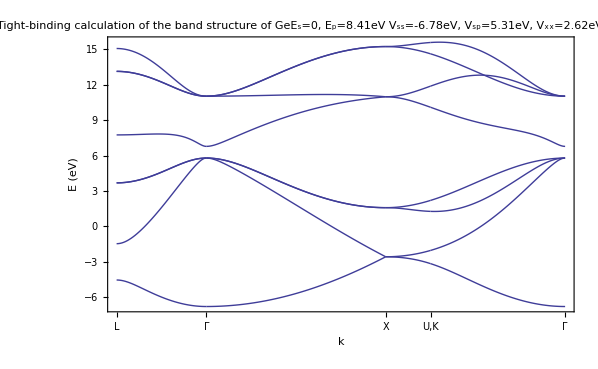

```mathematica
result=Show[plot1,plot2,plot3,plot4,
PlotRange->{{-0.5,2.0},All},Frame->True,
Axes->{True,False},
GridLines->{{-1/2,0,1,5/4,2},Automatic},
GridLinesStyle->{Directive[Thickness[0.001],Red],Gray},
FrameTicks->{{Automatic,Automatic},{{{-1/2,Style["L",FontSize->15]},{0,Style["Γ",FontSize->15]},{1,Style["X",FontSize->15]},{5/4,Style["U,K",FontSize->15]},{2,Style["Γ",FontSize->15]}},None}},
FrameLabel->{Style["k",FontSlant->Italic,FontWeight->Bold,FontSize->15],Style["E (eV)",FontSize->15,FontFamily->Times,FontSlant->Italic]},
PlotLabel->Row[{Style["Tight-binding calculation of the band structure of Ge",FontSize->25,FontFamily->Times],
Style["E_s=0, E_p=8.41eV\n V_ss=-6.78eV, V_sp=5.31eV, V_xx=2.62eV, V_xy=6.82eV",FontSize->20,FontFamily->Times]},"\n"]]
```

```mathematica
result=%220;
Export["Si.eps",result,ImageSize->100]
```

Si.eps